```mathematica
FullSimplify[Solve[{bsq==B^2-El^2,edotb==El*B},{El,B}]]
```

{{El→-(√2 edotb)/(√(bsq-√(bsq^2+4 edotb^2))),B→-(√(bsq-√(bsq^2+4 edotb^2)))/(√2)},{El→(√2 edotb)/(√(bsq-√(bsq^2+4 edotb^2))),B→(√(bsq-√(bsq^2+4 edotb^2)))/(√2)},{El→(√2 edotb)/(√(bsq+√(bsq^2+4 edotb^2))),B→(√(bsq+√(bsq^2+4 edotb^2)))/(√2)},{El→-(√2 edotb)/(√(bsq+√(bsq^2+4 edotb^2))),B→-(√(bsq+√(bsq^2+4 edotb^2)))/(√2)}}

```mathematica
f=HeavisideTheta[x/dx+1/2]*(1-HeavisideTheta[x/dx-1/2])
```

(1-HeavisideTheta[-1/2+x/dx]) HeavisideTheta[1/2+x/dx]

(1-HeavisideTheta[-1/2+x]) HeavisideTheta[1/2+x]

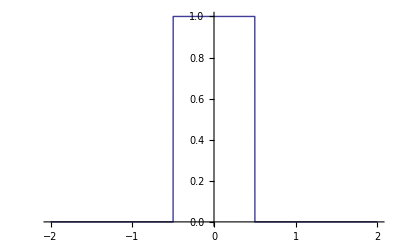

```mathematica
plotf=f//.{dx->1}
Plot[plotf,{x,-2,2}]
```

```mathematica
ftilde=FullSimplify[FourierTransform[f,x,w]//.{w->2*Pi*freqdx/dx},{dx>0}]
```

(dx Sin[freqdx π])/(√2 freqdx π^(3/2))

Sin[freqdx π]/(√2 freqdx π^(3/2))

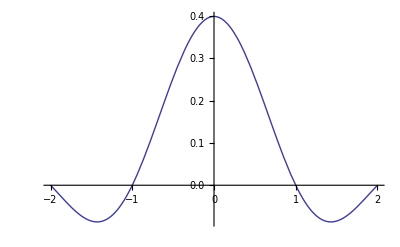

```mathematica
plotftilde=ftilde//.{dx->1}
Plot[plotftilde,{freqdx,-2,2}]
```

```mathematica
FindRoot[plotftilde==0,{freqdx,1}]
```

{freqdx→1.}

```mathematica
5*15
```

75

```mathematica
200/60.
```

3.33333

```mathematica
(* Generalized compact sin function *)
```

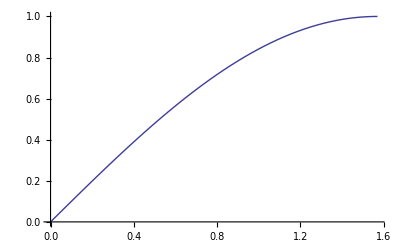

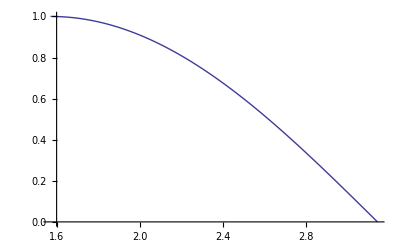

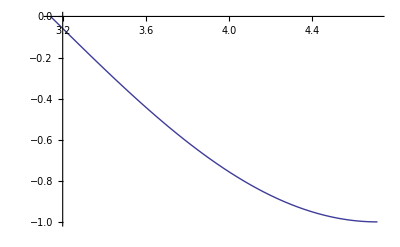

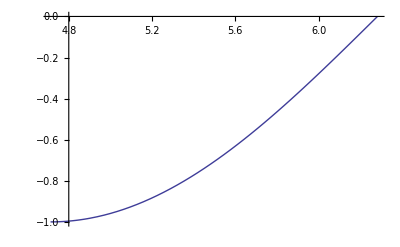

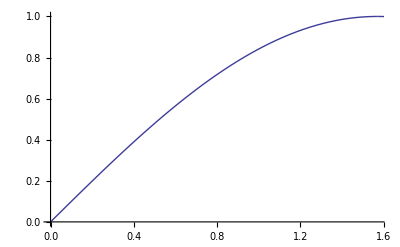

```mathematica
f1=Plot[Sin[x],{x,0,Pi/2}]
f2=Plot[Sin[Pi-x],{x,Pi/2,Pi}]
f3=Plot[-Sin[x-Pi],{x,Pi,3*Pi/2}]
f4=Plot[-Sin[2*Pi-x],{x,3*Pi/2,2*Pi}]
Show[f1,f2,f3,f4]
```

```mathematica
Mod[-2,4]
```

2

```mathematica
yap=a+b*x+c*x^2
fun=1/Sqrt[1+yap^2]
Series[fun,{x,0,3}]
```

a+b x+c x^2

1/(√(1+(a+b x+c x^2)^2))

1/(√(1+a^2))-(a b x)/((1+a^2)^(3/2))+((-b^2+2 a^2 b^2-2 a c-2 a^3 c) x^2)/(2 (1+a^2)^(5/2))+((3 a b^3-2 a^3 b^3-2 b c+2 a^2 b c+4 a^4 b c) x^3)/(2 (1+a^2)^(7/2))+O[x]^4